```mathematica
aaa=Range[50]*2
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100}

```mathematica
aaa[[5;;10]]
```

{10,12,14,16,18,20}

```mathematica
complexList222=Range/@Range[6]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6}}

```mathematica
f/@Range[6]
```

{15,15,15,15,15,15}

```mathematica
Range[#]&/@Range[6]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6}}

```mathematica
Map[Range,Range[6]]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6}}

```mathematica
Map[Range,Range[6]]//Trace
```

{{Range[6],{1,2,3,4,5,6}},Range/@{1,2,3,4,5,6},{Range[1],Range[2],Range[3],Range[4],Range[5],Range[6]},{Range[1],{1}},{Range[2],{1,2}},{Range[3],{1,2,3}},{Range[4],{1,2,3,4}},{Range[5],{1,2,3,4,5}},{Range[6],{1,2,3,4,5,6}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6}}}

```mathematica
Map[Range,Range[6]]//FullForm
```

List[List[1],List[1,2],List[1,2,3],List[1,2,3,4],List[1,2,3,4,5],List[1,2,3,4,5,6]]

```mathematica
Map[Range,Range[6]]//TracePrint
```

Range/@Range[6]

Map

Range

Range[6]

Range

6

{1,2,3,4,5,6}

Range/@{1,2,3,4,5,6}

{Range[1],Range[2],Range[3],Range[4],Range[5],Range[6]}

List

Range[1]

Range

1

{1}

Range[2]

Range

2

{1,2}

Range[3]

Range

3

{1,2,3}

Range[4]

Range

4

{1,2,3,4}

Range[5]

Range

5

{1,2,3,4,5}

Range[6]

Range

6

{1,2,3,4,5,6}

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6}}

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6}}

```mathematica
Map[Range,Range[6]]//TraceScan
```

TraceScan::argbu: TraceScan called with 1 argument; between 2 and 4 arguments are expected.

TraceScan[Range/@Range[6]]

```mathematica
myExtractFunction[listAll_,element_]:=Extract[listAll,Map[Most,Position[listAll,element]]]
```

```mathematica
myExtractFunction[complexList222,5]
```

{{1,2,3,4,5},{1,2,3,4,5,6}}

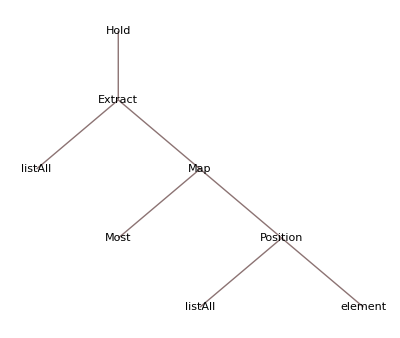

```mathematica
TreeForm[Hold[Extract[listAll,Map[Most,Position[listAll,element]]]]]
```

```mathematica
Position[complexList222,5]
```

{{5,5},{6,5}}

```mathematica
Map[Most,{{5,5},{6,5}}]
```

{{5},{6}}

```mathematica
Extract[complexList222,{{5},{6}}]
```

{{1,2,3,4,5},{1,2,3,4,5,6}}

```mathematica
Extract[complexList222,Map[Most,Position[complexList222,5]]]
```

{{1,2,3,4,5},{1,2,3,4,5,6}}

```mathematica
myExtractFunction[complexList222,4]
```

{{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6}}

```mathematica
complexList222//MatrixForm
```

({1}
{1,2}
{1,2,3}
{1,2,3,4}
{1,2,3,4,5}
{1,2,3,4,5,6})

## Write a small function which allows you to extract all sublists whose length is Odd.

```mathematica
myExtractFunction[listAll_,element_]:=Extract[listAll,Map[Most,Position[listAll,element]]]
```

```mathematica
complexList222
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6}}

```mathematica
Map[Length,complexList222]
```

{1,2,3,4,5,6}

```mathematica
OddQ[Map[Length,complexList222]]
```

{True,False,True,False,True,False}

```mathematica
Pick[complexList222,OddQ[Map[Length,complexList222]]]
```

{{1},{1,2,3},{1,2,3,4,5}}

```mathematica
allOddList[listAll1_]:=Pick[listAll1,OddQ[Map[Length,complexList222]]]
```

```mathematica
allOddList[complexList222]
```

{{1},{1,2,3},{1,2,3,4,5}}

## 另一种方法：

```mathematica
Position[OddQ[Map[Length,complexList222]],True]
```

{{1},{3},{5}}

```mathematica
Position[OddQ[Length[#]&/@complexList222],True]
```

{{1},{3},{5}}

```mathematica
Extract[complexList222,Position[OddQ[Map[Length,complexList222]],True]]
```

{{1},{1,2,3},{1,2,3,4,5}}

```mathematica
anotherFunction[a_]:=Extract[a,Position[OddQ[Length[#]&/@complexList222],True]]
```

```mathematica
anotherFunction[complexList222]
```

{{1},{1,2,3},{1,2,3,4,5}}

## 也就是说，pick和Extract[...,position[...,True]]等价

```mathematica
testList=RandomInteger[{4,20},20]
```

{5,7,14,6,18,18,20,9,12,18,18,4,9,11,11,19,12,19,16,6}

## 1) Find the largest and the smallest elements in the list above 2) Find the 5 largest and the 5 smallest elements in the list above 3) Find”moving maximum”in the list above. I t means that you take an element (the first one). Then the second element you will extract should be bigger than the first one.Then the third elelment you extract should be bigger than the second one,etc. Like this: inputList=[2,7,4,9,6,3,10] result=[2,7,9,10] 4)Sort the elements of the original list a increasing and decreasing numbers.

```mathematica
Max[testList]
```

20

```mathematica
Min[testList]
```

4

```mathematica
Sort[testList]
```

{4,5,6,6,7,9,9,11,11,12,12,14,16,18,18,18,18,19,19,20}

```mathematica
Take[Sort[testList],5]
```

{4,5,6,6,7}

```mathematica
Take[Sort[testList],-5]
```

{18,18,19,19,20}

## 3

```mathematica
testList
```

{5,7,14,6,18,18,20,9,12,18,18,4,9,11,11,19,12,19,16,6}

```mathematica
aaa=First[testList]
```

5

```mathematica
#1>First[testList]&/@testList
```

{False,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True}

```mathematica
Pick[testList,#1>First[testList]&/@testList]
```

{7,14,6,18,18,20,9,12,18,18,9,11,11,19,12,19,16,6}

```mathematica
a=First[Pick[testList,#1>First[testList]&/@testList]]
```

7

```mathematica
a=First[Pick[testList,#1>a&/@testList]]
```

14

```mathematica
f[x_]:=First[Pick[testList,#1>x&/@testList]]
```

```mathematica
f[7]
```

14

```mathematica
f[10]
```

14

```mathematica
NestList[f,First[Pick[testList,#1>First[testList]&/@testList]],3]
```

{7,14,18,20}

```mathematica
FixedPointList[f,First[Pick[testList,#1>First[testList]&/@testList]]]
```

First::nofirst: {} has zero length and no first element.

{7,14,18,20,First[{}],First[{}]}

```mathematica
finalResult=Prepend[FixedPointList[f,First[Pick[testList,#1>First[testList]&/@testList]]],First[testList]]//Most//Most
```

First::nofirst: {} has zero length and no first element.

{5,7,14,18,20}

## 尝试着变成函数

```mathematica
finalResult[x_]:=Prepend[FixedPointList[f,First[Pick[x,#1>First[x]&/@x]]],First[x]]//Most//Most
```

SetDelayed::write: Tag List in {5,7,14,18,20}[x_] is Protected.

$Failed

```mathematica
testList2={5,351,56,35,1,35,13,51,3,84,3,96,45,65251,,854,3184,654,6,687,3521,98}
```

{5,351,56,35,1,35,13,51,3,84,3,96,45,65251,Null,854,3184,654,6,687,3521,98}

```mathematica
finalResult[testList2]
```

{5,7,14,18,20}[{5,351,56,35,1,35,13,51,3,84,3,96,45,65251,Null,854,3184,654,6,687,3521,98}]

```mathematica
Do[Print[a=First[Pick[testList,#1>a&/@testList]]],3]
```

18

20

First::nofirst: {} has zero length and no first element.

First[{}]

## 4，Philippe’s answer

```mathematica
Clear[a] 
Clear[b]
```

```mathematica
testList
```

{5,7,14,6,18,18,20,9,12,18,18,4,9,11,11,19,12,19,16,6}

```mathematica
{1,4,10.2,100}/.x_Integer->x^2
```

{1,16,10.2,10000}

```mathematica
testList/.{a___,b_,c___,d_,e___}/;b>d->{a,d,c,b,e}
```

{4,7,14,6,18,18,20,9,12,18,18,5,9,11,11,19,12,19,16,6}

```mathematica
%/.{a___,b_,c___,d_,e___}/;b>d->{a,d,c,b,e}
```

{4,6,14,7,18,18,20,9,12,18,18,5,9,11,11,19,12,19,16,6}

```mathematica
%/.{a___,b_,c___,d_,e___}/;b>d->{a,d,c,b,e}
```

{4,5,14,7,18,18,20,9,12,18,18,6,9,11,11,19,12,19,16,6}

```mathematica
%/.{a___,b_,c___,d_,e___}/;b>d->{a,d,c,b,e}
```

{4,5,7,14,18,18,20,9,12,18,18,6,9,11,11,19,12,19,16,6}

```mathematica
%/.{a___,b_,c___,d_,e___}/;b>d->{a,d,c,b,e}
```

{4,5,6,14,18,18,20,9,12,18,18,7,9,11,11,19,12,19,16,6}

```mathematica
%/.{a___,b_,c___,d_,e___}/;b>d->{a,d,c,b,e}
```

{4,5,6,9,18,18,20,14,12,18,18,7,9,11,11,19,12,19,16,6}

```mathematica
%/.{a___,b_,c___,d_,e___}/;b>d->{a,d,c,b,e}
```

{4,5,6,7,18,18,20,14,12,18,18,9,9,11,11,19,12,19,16,6}

```mathematica
testList//.{a___,b_,c___,d_,e___}/;b>d->{a,d,c,b,e}
```

{4,5,6,6,7,9,9,11,11,12,12,14,16,18,18,18,18,19,19,20}

## 3 的真正解法

```mathematica
testList//.{a___,b_,c___,d_,e___}/;d<b->{a,b,c,e}
```

{5,7,14,18,18,20}

```mathematica
testList//.{a___,b_,c___,d_,e___}/;d<=b->{a,b,c,e}
```

{5,7,14,18,20}

```mathematica
{10,100,1000,10000}/.x_->x*RandomReal[]
```

{8.87824,88.7824,887.824,8878.24}

```mathematica
{10,100,1000,10000}/.x_:>x*RandomReal[]
```

{0.91024,9.1024,91.024,910.24}

```mathematica
{10,100,1000,10000}/.x_Integer:>x*RandomReal[]
```

{9.08114,81.354,241.51,3390.39}